Plot a line integral around a parallelopiped path

```mathematica
<<peeters` ;
<<MaTeX`

SetOptions[MaTeX,"Preamble"->{"\\usepackage{xcolor,txfonts}","\\definecolor{BlueDarker}{HTML}{0000AA}","\\definecolor{RedDarker}{HTML}{AA0000}","\\definecolor{PurpleDarker}{HTML}{550055}","\\definecolor{OrangeDarker}{HTML}{AA5500}","\\definecolor{GreenDarker}{HTML}{00AA00}"},
"FontSize" -> 14]
peeters`setGitDir[ "../project/figures/classicalmechanics" ]
```

{BasePreamble→{\usepackage{lmodern,exscale},\usepackage{amsmath,amssymb}},Preamble→{\usepackage{xcolor,txfonts},\definecolor{BlueDarker}{HTML}{0000AA},\definecolor{RedDarker}{HTML}{AA0000},\definecolor{PurpleDarker}{HTML}{550055},\definecolor{OrangeDarker}{HTML}{AA5500},\definecolor{GreenDarker}{HTML}{00AA00}},DisplayStyle→True,ContentPadding→True,LineSpacing→{1.2,0},FontSize→14,Magnification→1,LogFileFunction→None,TeXFileFunction→None}

\\wsl$\Ubuntu\home\pjoot\project\figures\classicalmechanics

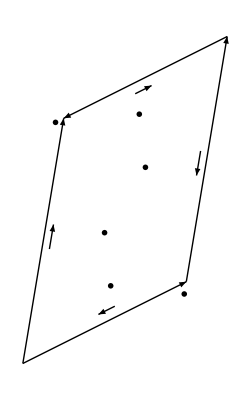

```mathematica
ClearAll[o,a,b]
o ={0,0};
a = {1,0.5};
b = {0.25,1.5};
e = 0.1;

p = Graphics[{
Thick,
Arrow[{o,a}],
Arrow[{o,b}],
Arrow[{a,a+b}],
Arrow[{a + b,b}],

Arrow[{(1+e)a/2 +(e/2) b, (1-e)a/2 + (e/2) b}],
Arrow[{(1-e)a/2 +(1- e/2) b, (1+e)a/2 +(1- e/2) b}],
Arrow[{(1-e)b/2 +(e/2) a, (1+e)b/2 + (e/2) a}],
Arrow[{(1+e)b/2 +(1- e/2) a, (1-e)b/2 +(1- e/2) a}],

Text[ MaTeX["a"], a - (e/2) b],
Text[ MaTeX["b"], b - (e/2) a],

Text[ MaTeX["F(u,1) (+a du) G(u,1)"], a/2 +(1- 1.5e) b],
Text[ MaTeX["F(u,0) (-a du) G(u,0)"], a/2 +(0+ 1.5e) b],

Text[ MaTeX["F(1,v) (-b dv) G(1,v)"], b(e + 1/2) +(1- 4e) a],
Text[ MaTeX["F(0,v) (+b dv) G(0,v)"], b(-e + 1/2) +(0+ 4e) a]

}]
```

```mathematica
peeters`exportForLatex["lineIntegralAroundParallelopipedFig1", p]
```

{lineIntegralAroundParallelopipedFig1.eps,lineIntegralAroundParallelopipedFig1pn.png}

```mathematica
ClearAll[carrow]
(* arrow centered about a point with len size on each side of the center point in the unit direction associated with dir. *)
carrow[c_, dir_, len_] :=Arrow[{c - (dir//Normalize) len, c + (dir//Normalize) len}];
```

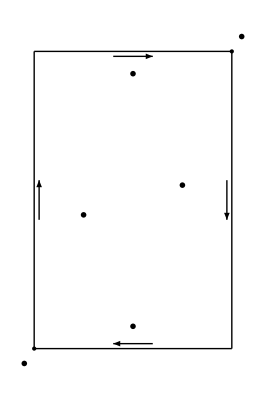

```mathematica
ClearAll[o,a,b, e]
o ={0,0};
a = {1,0};
b = {0,1.5};
e = 0.05;

p2 = Graphics[{
Thick,
Line[{o,a}],
Line[{o,b}],
Line[{a,a+b}],
Line[{a + b,b}],

PointSize ->Large,
Point[o],
Point[a+b],

carrow[ a/2+(e/2) (b//Normalize),-a,0.1],
carrow[ b +  a/2-(e/2) (b//Normalize),a,0.1],
carrow[ b/2+(e/2) (a//Normalize),b,0.1],
carrow[ a + b/2-(e/2) (a//Normalize),-b,0.1],

Text[ MaTeX["(x^1(1),x^2(1))"], (1+e) (a+b)],
Text[ MaTeX["(x^1(0),x^2(0))"], - e (a+b)],

Text[ MaTeX["dx^1 e_1 G(x^1,x^2(1))"], a/2 +(1- 1.5e) b],
Text[ MaTeX["-dx^1 e_1 G(x^1,x^2(0))"], a/2 +(0+ 1.5e) b],

Text[ MaTeX["-dx^2 e_2 G(x^1(1),x^2)"], b(e + 1/2) +(1- 5e) a],
Text[ MaTeX["dx^2 e_2 G(x^1(0),x^2)"], b(-e + 1/2) +(0+ 5e) a]

}]
```

```mathematica
peeters`exportForLatex["lineIntegralAroundRectangleFig1", p2]
```

{lineIntegralAroundRectangleFig1.eps,lineIntegralAroundRectangleFig1pn.png}

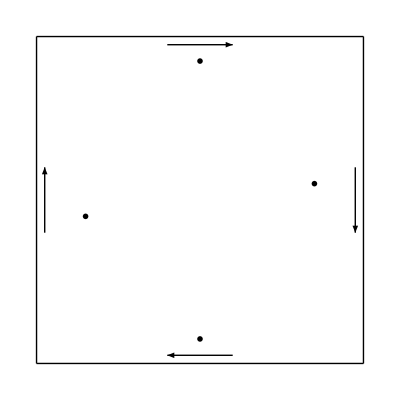

```mathematica
ClearAll[o,a,b, e]
o ={0,0};
a = {1,0};
b = {0,1};
e = 0.05;

p3 = Graphics[{
Thick,
Line[{o,a}],
Line[{o,b}],
Line[{a,a+b}],
Line[{a + b,b}],

carrow[ a/2+(e/2) (b//Normalize),-a,0.1],
carrow[ b +  a/2-(e/2) (b//Normalize),a,0.1],
carrow[ b/2+(e/2) (a//Normalize),b,0.1],
carrow[ a + b/2-(e/2) (a//Normalize),-b,0.1],

Text[ MaTeX["dx P(x,y_1)"], a/2 +(1- 1.5e) b],
Text[ MaTeX["-dx P(x,y_0)"], a/2 +(0+ 1.5e) b],

Text[ MaTeX["-dy Q(x_1,y)"], b(e + 1/2) +(1- 3e) a],
Text[ MaTeX["dy Q(x_0,y)"], b(-e + 1/2) +(0+ 3e) a]

}]
```

```mathematica
peeters`exportForLatex["GreensTheoremBoundaryFig1", p3]
```

{GreensTheoremBoundaryFig1.eps,GreensTheoremBoundaryFig1pn.png}

```mathematica
ClearAll[darrow]
(* arrow starting at a point with len size in the unit direction associated with dir. *)
darrow[c_, dir_, len_] :=Arrow[{c , c + (dir//Normalize) len}];
```

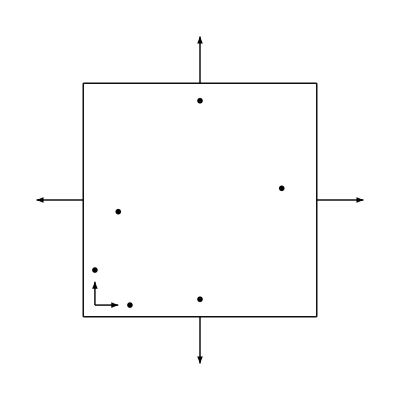

```mathematica
ClearAll[o,a,b, e]
o ={0,0};
a = {1,0};
b = {0,1};
e = 0.05;

p4 = Graphics[{
Thick,
Line[{o,a}],
Line[{o,b}],
Line[{a,a+b}],
Line[{a + b,b}],

darrow[ o + 0.05(a+b),a,0.1],
darrow[ o + 0.05(a+b),b,0.1],

darrow[ a/2,-b,0.2],
darrow[ b + a/2,b,0.2],
darrow[ a + b/2,a,0.2],
darrow[ b/2,-a,0.2],

Text[ MaTeX["\\mathbf{e}_1"],0.05b+0.2a],
Text[ MaTeX["\\mathbf{e}_2"],0.05a+0.2b],

Text[ MaTeX["\\mathbf{e}_2 dx G(x,y_1)"], a/2 +(1- 1.5e) b],
Text[ MaTeX["-\\mathbf{e}_2 dx G(x,y_0)"], a/2 +(0+ 1.5e) b],

Text[ MaTeX["\\mathbf{e}_1 dy G(x_1, y)"], b(e + 1/2) +(1- 3e) a],
Text[ MaTeX["-\\mathbf{e}_1 dy G(x_0, y)"], b(-e + 1/2) +(0+ 3e) a]

}]
```

```mathematica
peeters`exportForLatex["gradientOutWardsNormalFig1", p4]
```

{gradientOutWardsNormalFig1.eps,gradientOutWardsNormalFig1pn.png}

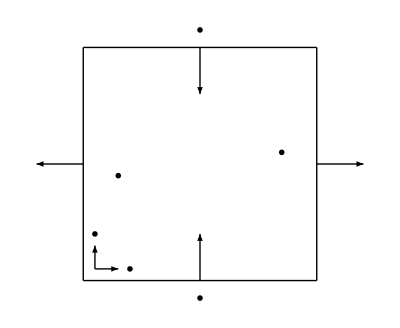

```mathematica
ClearAll[o,a,b, e]
o ={0,0};
a = {1,0};
b = {0,1};
e = 0.05;

p5 = Graphics[{
Thick,
Line[{o,a}],
Line[{o,b}],
Line[{a,a+b}],
Line[{a + b,b}],

darrow[ o + 0.05(a+b),a,0.1],
darrow[ o + 0.05(a+b),b,0.1],

darrow[ a/2,b,0.2],
darrow[ b + a/2,-b,0.2],
darrow[ a + b/2,a,0.2],
darrow[ b/2,-a,0.2],

Text[ MaTeX["\\gamma_0"],0.05b+0.2a],
Text[ MaTeX["\\gamma_1"],0.05a+0.2b],

Text[ MaTeX["-\\gamma_1 dt G(t,x_1)"], a/2 +(1+ 1.5e) b],
Text[ MaTeX["\\gamma_1 dt G(t,x_0)"], a/2 +(0- 1.5e) b],

Text[ MaTeX["\\gamma_0 dx G(t_1, x)"], b(e + 1/2) +(1- 3e) a],
Text[ MaTeX["-\\gamma_0 dx G(t_0, x)"], b(-e + 1/2) +(0+ 3e) a]

}]
```

```mathematica
peeters`exportForLatex["gradientOutWardsNormalSpaceTimeFig1", p5]
```

{gradientOutWardsNormalSpaceTimeFig1.eps,gradientOutWardsNormalSpaceTimeFig1pn.png}